```mathematica
(* Run to install FeynCalc 
<<FeynCalc`*)
```

```mathematica
Clear["Global`*"]
```

# Construct

## Do Wick’s contractions

```mathematica
(* Define the vertex of the interaction and propagator for the spin-1 massive field *)
Vertex[ω_,k_,mu_,nu_,rho_,sigma_]:=1/2(-(FV[ω,mu]*FV[k,nu]+FV[ω,nu]*FV[k,mu])MT[rho,sigma] + FV[ω,mu]*FV[k,rho]*MT[nu,sigma] + FV[ω,sigma]*FV[k,nu]*MT[mu,rho] + FV[ω,sigma]*FV[k,mu]*MT[nu,rho] +FV[ω,nu]*FV[k,rho]*MT[mu,sigma]-FV[ω,sigma]*FV[k,rho]*MT[mu,nu]+(M^2 + SP[ω,k])*(MT[mu,nu]*MT[rho,sigma] - MT[mu,rho]*MT[nu,sigma] - MT[mu,sigma]*MT[nu,rho]));

Prop[mu_,nu_,k_]:=MT[mu,nu] - (FV[k,mu]*FV[k,nu])/M^2;

(* Rules *)

(* rewrite  et similia *)
Separateql = {
Pair[Momentum[l],Momentum[l]]:>Pair[LorentzIndex[l6],LorentzIndex[l7]]*Pair[LorentzIndex[l6],Momentum[l]]*Pair[LorentzIndex[l7],Momentum[l]],

Pair[Momentum[l],Momentum[q*x]]:>Pair[LorentzIndex[l1],LorentzIndex[q1]]*Pair[LorentzIndex[l1],Momentum[l]]*x*Pair[LorentzIndex[q1],Momentum[q]],
Pair[Momentum[x*q],Momentum[l]]:>Pair[LorentzIndex[q2],LorentzIndex[l2]]*Pair[LorentzIndex[l2],Momentum[l]]*x*Pair[LorentzIndex[q2],Momentum[q]],

Pair[Momentum[q],Momentum[l]]:>Pair[LorentzIndex[q3],LorentzIndex[l3]]*Pair[LorentzIndex[l3],Momentum[l]]*Pair[LorentzIndex[q3],Momentum[q]],
Pair[Momentum[l],Momentum[q]]:>Pair[LorentzIndex[l4],LorentzIndex[q4]]*Pair[LorentzIndex[l4],Momentum[l]]*Pair[LorentzIndex[q4],Momentum[q]]
};

ruleqx = {
(* separate  *)
Pair[LorentzIndex[a_],Momentum[x*q]]:>x*Pair[LorentzIndex[a],Momentum[q]],
Pair[LorentzIndex[a_],Momentum[q*x]]:>x*Pair[LorentzIndex[a],Momentum[q]],

(* separate  *)
Pair[Momentum[x*q],Momentum[x*q]]:>x^2 Pair[Momentum[q],Momentum[q]],
Pair[Momentum[x*q],Momentum[q]]:>x*Pair[Momentum[q],Momentum[q]],
Pair[Momentum[q],Momentum[x*q]]:>x*Pair[Momentum[q],Momentum[q]]
};

ruleηlq ={
Pair[LorentzIndex[a_],LorentzIndex[b_]]^2 Pair[LorentzIndex[a_],Momentum[l]]^2 Pair[LorentzIndex[b_],Momentum[q]]^2:>Pair[LorentzIndex[a],LorentzIndex[b]]* Pair[LorentzIndex[a],Momentum[l]]* Pair[LorentzIndex[b],Momentum[q]]*Pair[LorentzIndex[l5],LorentzIndex[q5]]* Pair[LorentzIndex[l5],Momentum[l]]* Pair[LorentzIndex[q5],Momentum[q]],

Pair[LorentzIndex[a_],LorentzIndex[b_]]^2 Pair[LorentzIndex[a_],Momentum[l]]^2 Pair[LorentzIndex[b_],Momentum[l]]^2:>Pair[LorentzIndex[a],LorentzIndex[b]]* Pair[LorentzIndex[a],Momentum[l]]* Pair[LorentzIndex[b],Momentum[l]]*Pair[LorentzIndex[l8],LorentzIndex[l9]]* Pair[LorentzIndex[l8],Momentum[l]]* Pair[LorentzIndex[l9],Momentum[l]]
};

ruleϵL = {
(* separate  *)
Pair[LorentzIndex[a_],Momentum[ϵ*l]]:>ϵ*Pair[LorentzIndex[a],Momentum[l]],
Pair[LorentzIndex[a_],Momentum[l*ϵ]]:>ϵ*Pair[LorentzIndex[a],Momentum[l]],

(* separate  *)
Pair[Momentum[ϵ*l],Momentum[ϵ*l]]:>ϵ^2 Pair[Momentum[l],Momentum[l]],
Pair[Momentum[ϵ*l],Momentum[l]]:>ϵ*Pair[Momentum[l],Momentum[l]],
Pair[Momentum[l],Momentum[ϵ*l]]:>ϵ*Pair[Momentum[l],Momentum[l]]
};
```

```mathematica
(* Costruct the numerator *)
Vertex1= Vertex[q-l - x*q,l + x*q,μ,ν,α,λ];
Prop1 = Prop[α,τ,l + x*q - q];
firstVP = Contract[Vertex1*Prop1];

Vertex2 = Vertex[l + x*q-q,-l - x*q,ρ,σ,τ,β];
Prop2 = Prop[λ,β,l+x*q];
secondVP = Contract[Vertex2*Prop2];

NumeratorV = Contract[firstVP*secondVP];

(* with molteplicity 2 *)
Numtot=Collect2[2*NumeratorV,MT,FV] // Simplify;

(* Even part *)
NumMinus = Numtot /. l->-l;
NumEven = (Numtot + NumMinus)/2 // Simplify;

NumeratoreFinale = Collect2[((NumEven//.ruleqx)//.Separateql )//.ruleηlq// Simplify,MT,FV];
NumFinϵ = NumeratoreFinale /. l->ϵ*l;

(* The expression to work with *)
NumFin = Collect2[(NumFinϵ//. ruleϵL )//Simplify,MT,FV];
```

## Extract terms

```mathematica
(* Extract the costant part *)
zeroTerm = NumFin /. ϵ->0 // Simplify;

(* Work with the dipendent part *)
NumL = Collect2[(NumFin - zeroTerm // Simplify),MT,FV];

(* check it does not contain costant terms *)
Print["\n (should be zero): ",NumL /. ϵ->0]

(* Terms with 2  : *)
NumLϵ = NumL/ϵ^2;
ϵ2Term =Collect2[NumLϵ/.ϵ->0//Simplify,MT,FV];

(* Terms with 4  :  *)
newNumL = NumL - ϵ^2 * ϵ2Term //Simplify;
newNumLϵ = newNumL/ϵ^4;
ϵ4Term = Collect2[newNumLϵ/.ϵ->0 //Simplify,MT,FV];

(* check that we have taken all the terms *)
Print["\n (should be zero): ",(NumFin - zeroTerm - ϵ^2 ϵ2Term- ϵ^4 ϵ4Term) //Simplify]
```

(should be zero): 0

(should be zero): 0

## Integrate

```mathematica
n = 2;
d = 4 - ϵ;

Δ= x(x-1)SP[q,q] + M^2;
```

```mathematica
S[mu_,nu_,rho_,sigma_]:=MT[mu,nu]*MT[rho,sigma] + MT[mu,rho]*MT[nu,sigma] + MT[mu,sigma]*MT[nu,rho];

(* substitute  *)
RuleS ={
Pair[LorentzIndex[a_],Momentum[l]]*Pair[LorentzIndex[b_],Momentum[l]]*Pair[LorentzIndex[c_],Momentum[l]]*Pair[LorentzIndex[d_],Momentum[l]]:>S[a,b,c,d]
};
```

```mathematica
I4 = (-1)^n Simplify[Normal[Series[Gamma[n-d/2- 2]/Gamma[n] Δ^(d/2+2-n)/(4π)^(d/2),{ϵ,0,0}]]];
term4 = Contract[Collect[ϵ4Term,l]//.RuleS]//Simplify;
I4term = I4*1/4*term4 //Simplify;
```

```mathematica
(* substitute  *)
Ruleη = {
Pair[LorentzIndex[a_],Momentum[l]]*Pair[LorentzIndex[b_],Momentum[l]]:>Pair[LorentzIndex[a],LorentzIndex[b]]
};
```

```mathematica
I2 = (-1)^(n-1)  Simplify[Normal[Series[Gamma[n-d/2- 1]/Gamma[n] Δ^(d/2+1-n)/(4π)^(d/2),{ϵ,0,0}]]];
term2 = Contract[Collect[ϵ2Term,l]//.Ruleη]//Simplify;
I2term = I2*1/2*term2;
```

```mathematica
Int[α_] := (-1)^(n+α) Simplify[Normal[Series[(Gamma[n-d/2- α]Gamma[d/2+ α])/(Gamma[n]Gamma[d/2]) Δ^(d/2+α-n)/(4π)^(d/2),{ϵ,0,0}]]];
```

```mathematica
I0term = Int[0]*zeroTerm;
```

```mathematica
(* The result after integration in  *)
FinalResult = I4term + I2term + I0term // Simplify;
```

## Real and Imaginary part of the Tensor

```mathematica
serieResult = Series[FinalResult,{ϵ,0,0}];

(* consider the  part of FinalResult *)
NoPolesPart = SeriesCoefficient[serieResult,0];

(*
(* Integrate to extract both the Real and Imaginary part *)
TensorFinal = Integrate[NoPolesPart,{x,0,1}];

(* Assume  *)
Πtensor = Simplify[TensorFinal,Assumptions->SP[q,q]<0];

subX = Πtensor/.Log[SP[q,q]]->X //Simplify;
(* when  has  the imaginary part is  *)
Imtens = subX/. X->-ⅈ*π //Simplify;

(* Look at the expression and extract by hand the imaginary part, which we define in the next step
Imtensnew = Collect[Imtens,π] //StandardForm;
*)*)
```

## Other way: Taking the Imaginary part: sub

```mathematica
subLog = FinalResult/. Log[M^2+(-1+x) x SP[q,q]]->Log[z] // Simplify;
divLog = subLog/Log[z] // Simplify;
limLog = Limit[Limit[divLog,{z->∞}],{ϵ->0}];
resfin = π*limLog;
```

## Final result

```mathematica
x1 = 1/2-1/2 √((-4 M^2+SP[q,q])/SP[q,q]) ;
x2 = 1/2+1/2 √((-4 M^2+SP[q,q])/SP[q,q]);
Πtensor = Integrate[resfin,{x,x1,x2}]//Simplify;
ΠTensor = Collect2[(Πtensor/. SP[q,q]->Pair[Momentum[q],Momentum[q]])//Simplify,MT,FV];
Print["\n Tensor = ",ΠTensor]
```

Tensor = 1/(1920 π (q̄)^4)√(((q̄)^2-4 M^2)/(q̄)^2) (-48 (ḡ)^μσ (ḡ)^νρ (q̄)^4 M^4-48 (ḡ)^μρ (ḡ)^νσ (q̄)^4 M^4-48 (ḡ)^μν (ḡ)^ρσ (q̄)^4 M^4-144 (q̄)^μ (q̄)^ν (q̄)^ρ (q̄)^σ M^4+48 (q̄)^μ (q̄)^ν (ḡ)^ρσ (q̄)^2 M^4+48 (q̄)^μ (ḡ)^νσ (q̄)^ρ (q̄)^2 M^4+48 (ḡ)^μσ (q̄)^ν (q̄)^ρ (q̄)^2 M^4+48 (q̄)^μ (ḡ)^νρ (q̄)^σ (q̄)^2 M^4+48 (ḡ)^μρ (q̄)^ν (q̄)^σ (q̄)^2 M^4+48 (ḡ)^μν (q̄)^ρ (q̄)^σ (q̄)^2 M^4-56 (ḡ)^μσ (ḡ)^νρ (q̄)^6 M^2-56 (ḡ)^μρ (ḡ)^νσ (q̄)^6 M^2+64 (ḡ)^μν (ḡ)^ρσ (q̄)^6 M^2-64 (q̄)^μ (q̄)^ν (ḡ)^ρσ (q̄)^4 M^2+56 (q̄)^μ (ḡ)^νσ (q̄)^ρ (q̄)^4 M^2+56 (ḡ)^μσ (q̄)^ν (q̄)^ρ (q̄)^4 M^2+56 (q̄)^μ (ḡ)^νρ (q̄)^σ (q̄)^4 M^2+56 (ḡ)^μρ (q̄)^ν (q̄)^σ (q̄)^4 M^2-64 (ḡ)^μν (q̄)^ρ (q̄)^σ (q̄)^4 M^2-48 (q̄)^μ (q̄)^ν (q̄)^ρ (q̄)^σ (q̄)^2 M^2-13 (ḡ)^μσ (ḡ)^νρ (q̄)^8-13 (ḡ)^μρ (ḡ)^νσ (q̄)^8+2 (ḡ)^μν (ḡ)^ρσ (q̄)^8-2 (q̄)^μ (q̄)^ν (ḡ)^ρσ (q̄)^6+13 (q̄)^μ (ḡ)^νσ (q̄)^ρ (q̄)^6+13 (ḡ)^μσ (q̄)^ν (q̄)^ρ (q̄)^6+13 (q̄)^μ (ḡ)^νρ (q̄)^σ (q̄)^6+13 (ḡ)^μρ (q̄)^ν (q̄)^σ (q̄)^6-2 (ḡ)^μν (q̄)^ρ (q̄)^σ (q̄)^6-24 (q̄)^μ (q̄)^ν (q̄)^ρ (q̄)^σ (q̄)^4)

## Check the Equivalence Goldstone Theorem

```mathematica
πtens[mu_,nu_]:=Pair[LorentzIndex[mu],Momentum[q]]*Pair[LorentzIndex[nu],Momentum[q]]- Pair[LorentzIndex[mu],LorentzIndex[nu]]*Pair[Momentum[q],Momentum[q]] ;
Πtens = 2*πtens[μ,ν]*πtens[ρ,σ] - 3*πtens[μ,ρ]*πtens[ν,σ] - 3*πtens[μ,σ]*πtens[ν,ρ];

Πgauge = 16/(7680 π^2)Πtens*π;
```

```mathematica
RuleMinimal = {
FV[q,a_]:>Pair[LorentzIndex[a],Momentum[q]],
MT[a_,b_]:>Pair[LorentzIndex[a],LorentzIndex[b]],
SP[q,q]:>Pair[Momentum[q],Momentum[q]]
};
```

```mathematica
ΠMinimal = (-(FV[q,μ] FV[q,ν] FV[q,ρ] FV[q,σ])/(240 π)+(FV[q,ρ] FV[q,σ] MT[μ,ν] SP[q,q])/(320 π)+(FV[q,ν] FV[q,σ] MT[μ,ρ] SP[q,q])/(1920 π)+(FV[q,ν] FV[q,ρ] MT[μ,σ] SP[q,q])/(1920 π)+(FV[q,μ] FV[q,σ] MT[ν,ρ] SP[q,q])/(1920 π)+(FV[q,μ] FV[q,ρ] MT[ν,σ] SP[q,q])/(1920 π)+(FV[q,μ] FV[q,ν] MT[ρ,σ] SP[q,q])/(320 π)-(MT[μ,σ] MT[ν,ρ] SP[q,q]^2)/(1920 π)-(MT[μ,ρ] MT[ν,σ] SP[q,q]^2)/(1920 π)-(MT[μ,ν] MT[ρ,σ] SP[q,q]^2)/(320 π)//.RuleMinimal)//Simplify;

ΠEGT = Collect2[Πgauge + ΠMinimal//Simplify,MT,FV];
ΠMassless = Collect2[ΠTensor/. M->0//Simplify,MT,FV];
Print["\n (should be zero): ",Collect2[ΠEGT -ΠMassless //Simplify,MT,FV]]
```

(should be zero): 0

# Towards the abundance estimation

## Tensorial perturbation

```mathematica
(* spatial metric and vector *)
η3D=-IdentityMatrix[3];
q3D={qx,qy,qz};

(* Rule to pass from FeynCalc expression to Table *)
Rule3DFeynToTable={
Pair[LorentzIndex[a_],LorentzIndex[b_]]:>η3D[[a,b]],

Pair[LorentzIndex[a_],Momentum[q]]:>q3D[[a]],
Pair[ExplicitLorentzIndex[a_],Momentum[q]]:>q3D[[a]],

Pair[Momentum[q],Momentum[q]]:>q0^2 - Sum[q3D[[i]]^2,{i,1,3}]
};

Rulefinal ={
qx^2+qy^2+qz^2:>Q^2,
-qx^2-qy^2-qz^2:>-Q^2,
(qx^2+qy^2+qz^2)^2:>Q^4,
(-qx^2-qy^2-qz^2)^2:>Q^4
 };
```

## Transverse, Traceless Projectors (and symmetric in and ) in 2D in 4D

```mathematica
(* Define the transverse traceless projector *)
qdir = q3D/Sqrt[Sum[q3D[[i]]^2 , {i,1,3}]];

PTT2D=Table[KroneckerDelta[i,j]-qdir[[i]]*qdir[[j]],{i,1,3},{j,1,3}];

PTT4D=Table[1/2(PTT2D[[i,k]]*PTT2D[[j,r]]+PTT2D[[i,r]]*PTT2D[[j,k]])-1/2 PTT2D[[i,j]]*PTT2D[[k,r]],{i,1,3},{j,1,3},{k,1,3},{r,1,3}];
```

## Define with tables

```mathematica
(* Map the result IMTensor and IMTensorMassive to a table, so easier to manage with indices and contractions *)

(* the Table has 3x3x3x3 dimension *)
TTtable3D=(Table[ΠTensor,{μ,1,3},{ν,1,3},{ρ,1,3},{σ,1,3}] //. Rule3DFeynToTable)//Simplify;
```

```mathematica
(* Projecting and summing over indices*)
fh=-(Sum[PTT4D[[i,j,k,r]]*TTtable3D[[i,j,k,r]],{i,1,3},{j,1,3},{k,1,3},{r,1,3}]//Simplify )//.Rulefinal //Simplify;

(* check if we get what known in the massless limit,we expect: From the gauge field   (see spin-1 massless TT.nb) and From the minimally coupled scalar field (see spin-0 TT.nb)*)
Print["\n (should be zero): ",(fh - 1/(8π)1/2((q0^2 - Q^2)^2)/30 - 1/(8π) 1/2(2(q0^2 - Q^2)^2)/5)/.M->0//Simplify]
```

(should be zero): 0

## Scalar perturbation

```mathematica
(* Contracting with deltas *)
fΘ =-( Sum[TTtable3D[[μ,μ,ρ,ρ]] ,{μ,1,3},{ρ,1,3}]//Simplify)//.Rulefinal//Simplify;

(* massless limit *)
Print["\n (should be zero): ",(1/(8π)1/2(-20 Q^2 q0^2 (1-6 ξ)^2+15 q0^4 (1-6 ξ)^2+Q^4 (7-80 ξ+240 ξ^2))/15+1/(8π) 1/2(4Q^4)/15-2*fΘ)/.{M->0,ξ->0}//Simplify]
```

(should be zero): 0

## Define with tables

```mathematica
η4D = {{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
q4D = {q0,qx,qy,qz};

q4Dlower = η4D.q4D;

(* Rule in 4D to pass from FeynCalc expression to Table *)
Rule4DFeynToTable={
Pair[LorentzIndex[a_],LorentzIndex[b_]]:>η4D[[a,b]],
Pair[ExplicitLorentzIndex[a_],ExplicitLorentzIndex[b_]]:>η4D[[a,b]],

Pair[LorentzIndex[a_],Momentum[q]]:>q4D[[a]],
Pair[ExplicitLorentzIndex[a_],Momentum[q]]:>q4D[[a]],

Pair[Momentum[q],Momentum[q]]:>q0^2 - Sum[q3D[[i]]^2,{i,1,3}]
};
```

```mathematica
(* Map the result IMTensor and IMTensorMassive to a table, so easier to manage with indices and contractions *)

(* the Table has 4x4x4x4 dimension *)
TTtable4D=(Table[ΠTensor,{μ,1,4},{ν,1,4},{ρ,1,4},{σ,1,4}] //. Rule4DFeynToTable) //Simplify;
```

## Scalar perturbation

```mathematica
(* Contracting with metric tensor (here is simpler using the FeynCalc expression)*)
fΣ=-((Contract[MT[μ,ν]*MT[ρ,σ]*ΠTensor]//Simplify)//.Rule4DFeynToTable)//.Rulefinal//Simplify;

(* check if we get what known in the massless limit
we expect zero contribute from the gauge field and a non-zero term from the minimally coupled scalar field, which is
(from spin-0 TT.nb putting ) *)
Print["\n (should be zero): ",(2*8π*fΣ/.M->0 ) - ((Q^2 -q0^2)^2)/2 //Simplify]
```

(should be zero): 0

## Vectorial perturbation

```mathematica
W3D = {Wx,Wy,Wz};
WT = Table[Sum[PTT2D[[i,j]]*W3D[[j]],{j,1,3}],{i,1,3}];

(* momentum space  *)
WTable = I*Table[q3D[[i]]*WT[[j]] + q3D[[j]]*WT[[i]],{i,1,3},{j,1,3}]//Simplify;

(* check of trasversality *)
Print["\n (should be zero): ",WT.q3D//Simplify]
```

(should be zero): 0

```mathematica
(* Contracting *)
fW=Sum[WTable[[i,j]]*WTable[[k,r]]*TTtable3D[[i,j,k,r]],{i,1,3},{j,1,3},{k,1,3},{r,1,3}] //Simplify ;

fWnew = (fW/. {(qz^2 (Wx^2+Wy^2)-2 qx qz Wx Wz-2 qy Wy (qx Wx+qz Wz)+qy^2 (Wx^2+Wz^2)+qx^2 (Wy^2+Wz^2))->Sum[q3D[[i]]^2,{i,1,3}]}//Simplify)//.Rulefinal //Simplify;

(* check if we get what known in the massless limit,we expect: From the gauge field   (see spin-1 massless TT.nb) and From the minimally coupled scalar field (see spin-0 TT.nb)*)
Print["\n (should be zero): ",(2*8π*fWnew - (2q0^2 Q^2(q0^2 - Q^2))/5 -  (q0^2 Q^2(q0^2 - Q^2))/30)/.M->0//Simplify]
```

(should be zero): 0

## Check with the result of the decay rate in spin-1.nb (massive)

```mathematica
(* Take the result from Γ estimations in spin-0.nb massive*)
Γestim = Import[FileNameJoin[{$HomeDirectory,"Documents","Rate estimations spin-1.wdx"}]];
subsInt = Γestim[[1]];

fΘestim = (2*8π*fΘ/.Q->q)/.subsInt//N;
fΣestim = (2*8π*fΣ/.Q->q)/.subsInt //N;
fWestim = (2*8π*fWnew/.Q->q)/.subsInt //N;
fhestim = (2*8π*fh/.Q->q)/.subsInt//N;

Print["\n Check scalar Θ (should be zero): ",Chop[fΘestim - Γestim[[2]] //Simplify]]
Print["\n Check scalar Σ (should be zero): ",Chop[fΣestim - 2*Γestim[[3]] //Simplify]]
Print["\n Check vectorial W (should be zero): ",Chop[fWestim - Γestim[[4]] //Simplify]]
Print["\n Check tensorial h (should be zero): ",Chop[fhestim - Γestim[[5]] //Simplify]]
```

Check scalar Θ (should be zero): 7.58814

Check scalar Σ (should be zero): 0

Check vectorial W (should be zero): 0

Check tensorial h (should be zero): 0

## Kernels and Plots

```mathematica
(* Kernels *)
funzh[q0_,Q_,M_]=2*8π*fh;
funzW[q0_,Q_,M_]=2*8π*fWnew;
funzΣ[q0_,Q_,M_]=2*8π*fΣ;
funzΘ[q0_,Q_,M_]=2*8π*fΘ;

(* Adimensional kernels  , *)
Funzhnew[x_,y_]:=funzh[q0,q,M]/.{M->x,q->y,q0->1};
FunzWnew[x_,y_]:=funzW[q0,q,M]/q^2/.{M->x,q->y,q0->1};
FunzΣnew[x_,y_]:=funzΣ[q0,q,M]/.{M->x,q->y,q0->1};
FunzΘnew[x_,y_]:=funzΘ[q0,q,M]/.{M->x,q->y,q0->1};

Print["\n fΘ = ",funzΘ[q0,q,M]]
Print["\n fΣ = ",funzΣ[q0,q,M]]
Print["\n fW = ",funzW[q0,q,M]]
Print["\n fh = ",funzh[q0,q,M]]

(* Check dimensionality *)
Print["\n (should be zero): ",Funzhnew[M/q0,q/q0]*q0^4 - funzh[q0,q,M]//Simplify]
Print["\n (should be zero): ",FunzWnew[M/q0,q/q0]*q0^4 q^2 - funzW[q0,q,M]//Simplify]
Print["\n (should be zero): ",FunzΣnew[M/q0,q/q0]*q0^4 - funzΣ[q0,q,M]//Simplify]
Print["\n (should be zero): ",FunzΘnew[M/q0,q/q0]*q0^4 - funzΘ[q0,q,M]//Simplify]
```

fΘ = (√((4 M^2+q^2-q0^2)/(q^2-q0^2)) (12 (8 q^4-20 q0^2 q^2+15 q0^4) M^4+4 (2 q^6-22 q0^2 q^4+35 q0^4 q^2-15 q0^6) M^2+(q^2-q0^2)^2 (11 q^4-20 q0^2 q^2+15 q0^4)))/(30 (q^2-q0^2)^2)

fΣ = 1/2 √((4 M^2)/(q^2-q0^2)+1) (12 M^4+4 (q^2-q0^2) M^2+(q^2-q0^2)^2)

fW = -(q^2 q0^2 √((4 M^2+q^2-q0^2)/(q^2-q0^2)) (48 M^4+56 (q0^2-q^2) M^2+13 (q^2-q0^2)^2))/(30 (q^2-q0^2))

fh = 1/30 √((4 M^2+q^2-q0^2)/(q^2-q0^2)) (48 M^4+56 (q0^2-q^2) M^2+13 (q^2-q0^2)^2)

(should be zero): 0

(should be zero): 0

(should be zero): 0

«1 more identical outputs»

```mathematica
(* From the Kernel factor  
From the condition *)
Reduce[(4x^2)/(y^2 - 1)+1>=0&&1-y^2>=4x^2&&x>0&&y>0,y]
```

0<x<1/2∧0<y≤√(1-4 x^2)

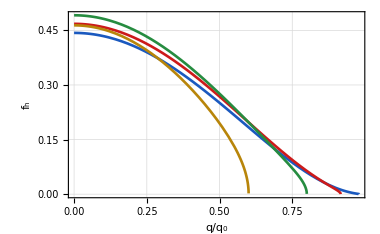

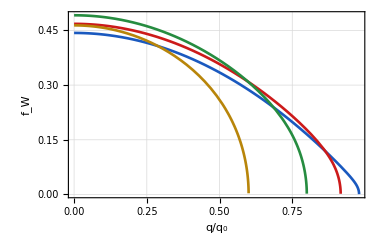

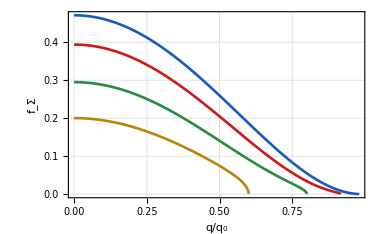

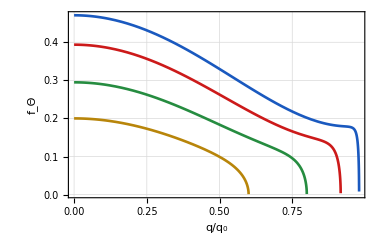

M / q_0

```mathematica
xvalues=Range[0.1,0.4,0.1]; (* 0< x <1/2*)

thesisColors={RGBColor[0.10,0.35,0.75],(*Blu Classico*)
RGBColor[0.80,0.10,0.10],(*Rosso*)
RGBColor[0.15,0.55,0.25],(*Verde Foresta*)
RGBColor[0.72,0.52,0.04],(*Giallo Scuro/Oro*)
RGBColor[0.45,0.15,0.55]  (*Viola/Indaco per il 5° valore*)
};

scientificPlotOptions[yLabel_]:=Sequence[PlotTheme->"Scientific",Frame->True,PlotStyle->Table[Directive[Thickness[0.005],thesisColors[[i]]],{i,Length[xvalues]}],FrameLabel->{Style[Row[{Style["q",Italic],"/",Subscript[Style["q",Italic],"0"]}],13,"Times"],Style[yLabel,14,"Times"]},PlotLabel->None,PlotLegends->None,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.92],Dashed],BaseStyle->{FontFamily->"Times",FontSize->11},FrameStyle->Directive[Black,Thickness[0.0012]],ImageSize->380,PlotRange->All,MaxRecursion->6,Exclusions->None];

 plotTensor=Plot[Evaluate[Table[ConditionalExpression[Funzhnew[x,y],y<=Sqrt[1-4x^2]],{x,xvalues}]],{y,10^-5,1},Evaluate@scientificPlotOptions[Subscript[Style["f",Italic],Style["h",Italic]]]];Print[plotTensor];

plotVector=Plot[Evaluate[Table[ConditionalExpression[FunzWnew[x,y],y<=Sqrt[1-4x^2]],{x,xvalues}]],{y,10^-5,1},Evaluate@scientificPlotOptions[Subscript[Style["f",Italic],Style["W",Italic]]]];Print[plotVector];

plotSigma=Plot[Evaluate[Table[ConditionalExpression[FunzΣnew[x,y],y<=Sqrt[1-4x^2]],{x,xvalues}]],{y,10^-5,1},Evaluate@scientificPlotOptions[Subscript[Style["f",Italic],Style["Σ",Italic]]]];Print[plotSigma];

 plotTheta=Plot[Evaluate[Table[ConditionalExpression[FunzΘnew[x,y],y<=Sqrt[1-4x^2]],{x,xvalues}]],{y,10^-5,1},Evaluate@scientificPlotOptions[Subscript[Style["f",Italic],Style["Θ",Italic]]]];Print[plotTheta]

legendStandaloneBox=Framed[Column[{Style[Row[{Style["M",Italic]," / ",Subscript[Style["q",Italic],"0"]}],12,Bold,FontFamily->"Times New Roman"],Spacer[6],LineLegend[thesisColors,Table[NumberForm[x,{2,1}],{x,xvalues}],LabelStyle->{FontFamily->"Times New Roman",FontSize->11,GrayLevel[0.15]},Spacings->{0.5,0.6},LegendMarkerSize->{20,3.5},LegendLayout->"Vertical"]},Alignment->Center],FrameStyle->Directive[GrayLevel[0.72],Thickness[0.0015]],Background->GrayLevel[0.98],RoundingRadius->4,FrameMargins->{{10,10},{8,10}} ];

Print[legendStandaloneBox]
(*
Export[FileNameJoin[{NotebookDirectory[],"Legend_spin1.pdf"}],legendStandaloneBox];
Export[FileNameJoin[{NotebookDirectory[],"Kernel_Tensor_spin1.pdf"}],plotTensor];
Export[FileNameJoin[{NotebookDirectory[],"Kernel_Vector_spin1.pdf"}],plotVector];
Export[FileNameJoin[{NotebookDirectory[],"Kernel_Sigma_spin1.pdf"}],plotSigma];
Export[FileNameJoin[{NotebookDirectory[],"Kernel_Theta_spin1.pdf"}],plotTheta];
*)
```

# Model for the Power spectrum of GW, sourced by a Order Phase-Transition

## Template: correlation modeled by the size of the bubbles

## , interested in , ,

```mathematica
(* Model Template *)
g[t_,n_]:=HeavisideTheta[t]HeavisideTheta[1/β-t](4β^2 t(1/β-t))^(n-1);
ftemplate[q_,t_,v_,n_]:=g[t,n](v t)^(3/2)√((1+((q v t)/3)^2)/(1+((q v t)/2)^2+((q v t)/3)^6));
fTDF[q0_,q_,n_]:=NIntegrate[ftemplate[q,t,vel,n]Exp[I q0 t]/.{β->1,vel->1},{t,0,1}];

Δh[q0_,q_,n_]:=q^3 Abs[fTDF[q0,q,n]]^2/((q0^2- q^2)^2);
```

```mathematica
funzh[q0_,q_,M_]:=1/30 √((4 M^2+q^2-q0^2)/(q^2-q0^2))(48 M^4+56 M^2(q0^2-q^2)+13(q^2-q0^2)^2);
```

## Integrations

```mathematica
(* Interpolated Integrand *)
Integrand[q0_,q_,M_,n_]:= funzh[q0,q,M]/q*Δh[q0,q,n]*(q0*Log[10])*(q*Log[10]);
(* integration over  and  *)
Nadim[M_,n_] := Sum[Integrand[10^lq0,10^lq,M,n],{lq0,Log10[2M]+0.05,3,0.05},{lq,-2,1/2 Log10[10^(2*lq0) - 4M^2],0.05}](0.05)^2//Quiet;
(* M should be < 500 β to not exceed 3 in  integral,
Note that  has a maximum value of 3 (for lq0 = 3 and M =0)*)
```

## Final abundance

```mathematica
ΩDM[n_,Mmin_,Mmax_,NM_]:=ParallelTable[{M,Nadim[M,n]},{M,Mmin,Mmax,(Mmax-Mmin)/NM}];
```

```mathematica
(*
ΩDMfinal1=Join[ΩDM[1.,0.01,10.,50],ΩDM[1.,12.,30,5]]//Quiet;
Nadimensional1 = ΩDMfinal1[[All,2]];
MΩ1 =ΩDMfinal1[[All,1]]; 

ΩDMfinal2=Join[ΩDM[2.,0.01,10.,50],ΩDM[2.,12.,30,5]]//Quiet;
Nadimensional2= ΩDMfinal2[[All,2]];
MΩ2 =ΩDMfinal2[[All,1]]; 

ΩDMfinal3=Join[ΩDM[3.,0.01,10.,50],ΩDM[3.,12.,30,5]]//Quiet;
Nadimensional3 = ΩDMfinal3[[All,2]];
MΩ3 =ΩDMfinal3[[All,1]]; 

(* Save the abundance into a file *)
Export[FileNameJoin[{$HomeDirectory,"Documents","Abundance spin-1 n1.wdx"}],ΩDMfinal1];
Export[FileNameJoin[{$HomeDirectory,"Documents","Abundance spin-1 n2.wdx"}],ΩDMfinal2];
Export[FileNameJoin[{$HomeDirectory,"Documents","Abundance spin-1 n3.wdx"}],ΩDMfinal3];

ΩDMfinalCSV1="Abundance spin-1 n1.csv";
Print["Saving data to: ",NotebookDirectory[],"\\",ΩDMfinalCSV1];
Export[ΩDMfinalCSV1,ΩDMfinal1];
ΩDMfinalCSV2="Abundance spin-1 n2.csv";
Print["Saving data to: ",NotebookDirectory[],"\\",ΩDMfinalCSV2];
Export[ΩDMfinalCSV2,ΩDMfinal2];
ΩDMfinalCSV3="Abundance spin-1 n3.csv";
Print["Saving data to: ",NotebookDirectory[],"\\",ΩDMfinalCSV3];
Export[ΩDMfinalCSV3,ΩDMfinal3];
*)

(* if you want to extract *)
ΩDMfinal1 = Import[FileNameJoin[{$HomeDirectory,"Documents","Abundance spin-1 n1.wdx"}]];
Nadimensional1 = ΩDMfinal1[[All,2]];
MΩ1 = ΩDMfinal1[[All,1]]; 

ΩDMfinal2 = Import[FileNameJoin[{$HomeDirectory,"Documents","Abundance spin-1 n2.wdx"}]];
Nadimensional2 = ΩDMfinal2[[All,2]];
MΩ2 = ΩDMfinal2[[All,1]]; 

ΩDMfinal3 = Import[FileNameJoin[{$HomeDirectory,"Documents","Abundance spin-1 n3.wdx"}]];
Nadimensional3 = ΩDMfinal3[[All,2]];
MΩ3 = ΩDMfinal3[[All,1]];
```

Power law fit: y = 4.32708 * x^-0.867611

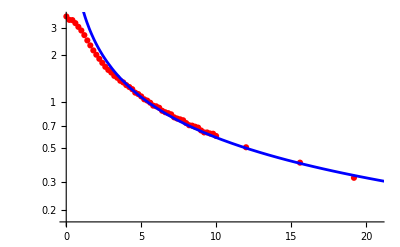

```mathematica
(* define the log data *)
logData1=Transpose[{MΩ1[[15;;]],Log[Nadimensional1[[15;;]]]}];

(* Fit : param1 + param2*Log[x]*)
logFit1=LinearModelFit[logData1,{1,Log[x]},x];

(* param1 + param2*Log[x] = param1 + Log[x^param2] = Log[E^param1] + Log[x^param2] = Log[E^param1 x^param2] = Log[A x^b]*)

(* Extract parameters *)
b1=logFit1["BestFitParameters"][[2]];
A1=Exp[logFit1["BestFitParameters"][[1]]];

Print["Power law fit: y = ",A1," * x^",b1];

(*4. To plot it over your ListLogPlot:*)
Show[ListLogPlot[Transpose[{MΩ1,Nadimensional1}],PlotStyle->Red],LogPlot[A1*x^b1,{x,Min[MΩ1],Max[MΩ1]},PlotStyle->Blue]]
```

Power law fit: y = 4.36931 * x^-2.7818

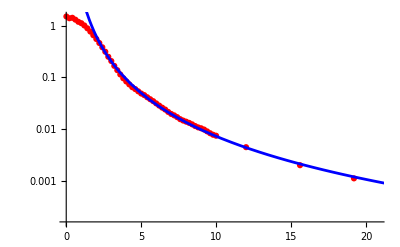

```mathematica
(* define the log data *)
logData2=Transpose[{MΩ2[[15;;]],Log[Nadimensional2[[15;;]]]}];

(* Fit : param1 + param2*Log[x]*)
logFit2=LinearModelFit[logData2,{1,Log[x]},x];

(* Extract parameters *)
b2=logFit2["BestFitParameters"][[2]];
A2=Exp[logFit2["BestFitParameters"][[1]]];

Print["Power law fit: y = ",A2," * x^",b2];

(*4. To plot it over your ListLogPlot:*)
Show[ListLogPlot[Transpose[{MΩ2,Nadimensional2}],PlotStyle->Red],LogPlot[A2*x^b2,{x,Min[MΩ2],Max[MΩ2]},PlotStyle->Blue]]
```

Power law fit: y = 48.9296 * x^-4.80768

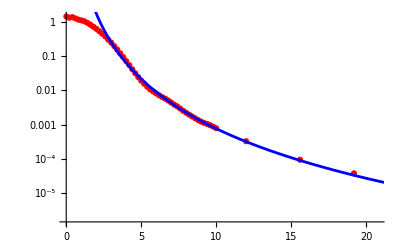

```mathematica
(* define the log data *)
logData3=Transpose[{MΩ3[[15;;]],Log[Nadimensional3[[15;;]]]}];

(* Fit : param1 + param2*Log[x]*)
logFit3=LinearModelFit[logData3,{1,Log[x]},x];

(* Extract parameters *)
b3=logFit3["BestFitParameters"][[2]];
A3=Exp[logFit3["BestFitParameters"][[1]]];
(* logFit3["ParameterErrors"] *)

Print["Power law fit: y = ",A3," * x^",b3];

(*4. To plot it over your ListLogPlot:*)
Show[ListLogPlot[Transpose[{MΩ3,Nadimensional3}],PlotStyle->Red],LogPlot[A3*x^b3,{x,Min[MΩ3],Max[MΩ3]},PlotStyle->Blue]]
```

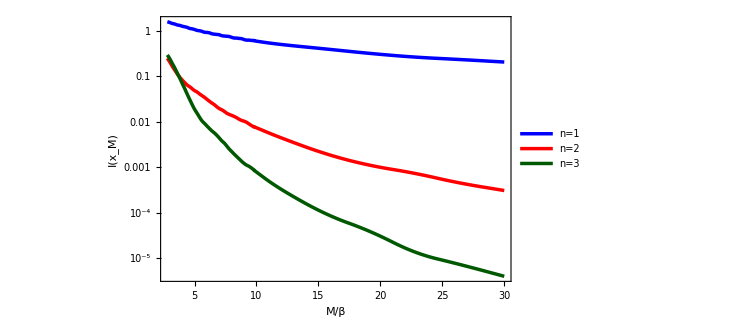

```mathematica
ListLogPlot[{Transpose[{MΩ1[[15;;]],Nadimensional1[[15;;]]}],Transpose[{MΩ2[[15;;]],Nadimensional2[[15;;]]}],Transpose[{MΩ3[[15;;]],Nadimensional3[[15;;]]}]},Joined->True,InterpolationOrder->2,PlotRange->All,AspectRatio->1/GoldenRatio,Frame->True,Axes->False,PlotStyle->{{Blue,AbsoluteThickness[2.5]},{Red,AbsoluteThickness[2.5]},{DarkGreen,AbsoluteThickness[2.5]}},FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],FrameLabel->{Style[DisplayForm[FormBox[RowBox[{FormBox["M",TraditionalForm],"/",FormBox["β",TraditionalForm]}],TraditionalForm]],FontSize->16],Style[DisplayForm[FormBox[RowBox[{"I","(",SubscriptBox["x","M"],")"}],TraditionalForm]],FontSize->16]},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.9],Dashed],PlotLegends->Placed[LineLegend[{Style[DisplayForm[FormBox[RowBox[{"n","=","1"}],TraditionalForm]],FontSize->13],Style[DisplayForm[FormBox[RowBox[{"n","=","2"}],TraditionalForm]],FontSize->13],Style[DisplayForm[FormBox[RowBox[{"n","=","3"}],TraditionalForm]],FontSize->13]},Background->White,LegendLabel->None,LegendMargins->6,LegendMarkerSize->20,LabelStyle->Directive[FontFamily->"Times"],Method->{"Frame"->True,"FrameStyle"->Directive[Black,AbsoluteThickness[1]]}],{0.82,0.60} ],ImageSize->540]
```

```mathematica
(* Standard Cosmologies parameters *)
T0=2.35*10^-13;        (* CMB temperature [GeV] *)
gS0=3.91;                        (* Today entropy degrees of freedom*)
ρc0=8.09*10^-47;     (* Today critical density/h^2 [GeV^4]*)
Mpl=2.43*10^18;        (* Reduced Planck mass [GeV] *)

(* At the Phase transition *)
Tstar=10^14;                                      (* Temperature [GeV] *)
gSstar=106.75;                                (* Degrees of freedom by Standard Model *)(* gtrue = 106.75 *)
Hstar=√(π^2/90*gSstar)Tstar^2/Mpl;   (* Hubble parameter *)

(* Redshift *)
RedshiftFactor=(gS0*T0^3)/(gSstar*Tstar^3);

(* 1PT parameters *)
βH = 100;                                    (* We assume no universe expansion, so  *)
βvalue=βH* Hstar;               (* Inverse time duration of 1PT [GeV] *)
velocity = 1;                           (* Bubble wall velocity (speed of light) *)
αheat=0.1;                                (* Latent heat  *)
kappa=0.05;                               (* Efficiency factor *)


ScaleFactorDim=βvalue^3(kappa*αheat)^2/(1 + αheat)^2*(Hstar/βvalue)^4*velocity^3; (* [Gev^3]*)


finalΩ1 =9/(4π^4)*RedshiftFactor*ScaleFactorDim* (MΩ1*βvalue*Nadimensional1)/ρc0; (* adimensional *)
finalΩ2 =9/(4π^4)*RedshiftFactor*ScaleFactorDim *(MΩ2*βvalue*Nadimensional2)/ρc0; (* adimensional *)
finalΩ3 =9/(4π^4)*RedshiftFactor*ScaleFactorDim *(MΩ3*βvalue*Nadimensional3)/ρc0; (* adimensional *)
```

```mathematica
frequencyToday = 10^-5 (gSstar/100)^(1/6)Tstar/100(βvalue/Hstar)
```

1.01095×10^9

## Plots

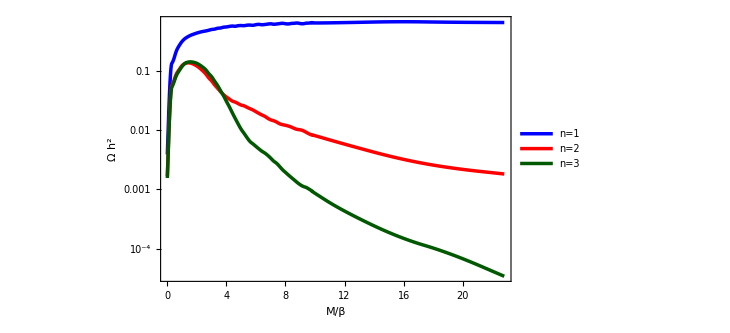

```mathematica
plotData1=Transpose[{MΩ1[[1;;55]],finalΩ1[[1;;55]]}];
plotData2=Transpose[{MΩ2[[1;;55]],finalΩ2[[1;;55]]}];
plotData3=Transpose[{MΩ3[[1;;55]],finalΩ3[[1;;55]]}];

scientificPlot=ListLogPlot[{plotData1,plotData2,plotData3},Joined->True,InterpolationOrder->2,PlotRange->All,AspectRatio->1/GoldenRatio,Frame->True,Axes->False,PlotStyle->{{Blue,AbsoluteThickness[2.5]},{Red,AbsoluteThickness[2.5]},{DarkGreen,AbsoluteThickness[2.5]}},FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],FrameLabel->{Style[DisplayForm[FormBox[RowBox[{FormBox["M",TraditionalForm],"/",FormBox["β",TraditionalForm]}],TraditionalForm]],FontSize->16],Style[DisplayForm[FormBox[RowBox[{"Ω",SuperscriptBox["h","2"]}],TraditionalForm]],FontSize->16]},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.9],Dashed],PlotLegends->Placed[LineLegend[{Style[DisplayForm[FormBox[RowBox[{"n","=","1"}],TraditionalForm]],FontSize->13],Style[DisplayForm[FormBox[RowBox[{"n","=","2"}],TraditionalForm]],FontSize->13],Style[DisplayForm[FormBox[RowBox[{"n","=","3"}],TraditionalForm]],FontSize->13]},Background->White,LegendLabel->None,LegendMargins->6,LegendMarkerSize->20,LabelStyle->Directive[FontFamily->"Times"],Method->{"Frame"->True,"FrameStyle"->Directive[Black,AbsoluteThickness[1]]}],{0.82,0.70} ],ImageSize->540]

Export[FileNameJoin[{NotebookDirectory[],"Abundance_spin-1_Plot.pdf"}],scientificPlot];
```

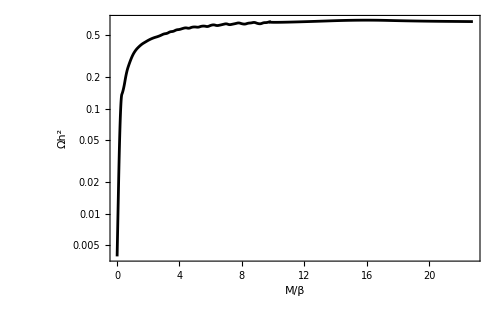

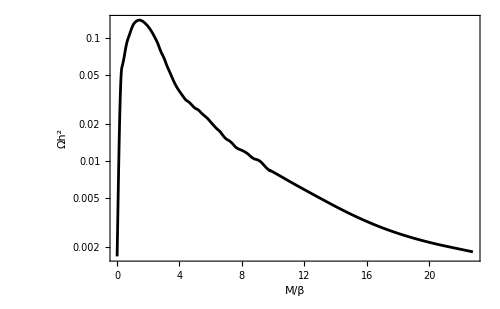

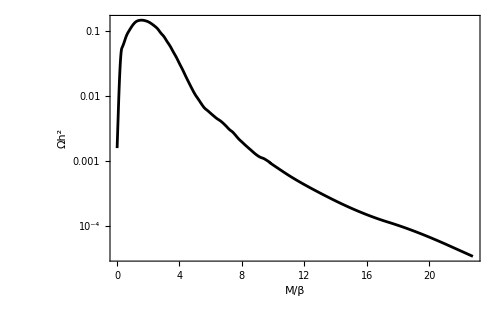

```mathematica
scientificPlot1=ListLogPlot[plotData1,Joined->True,InterpolationOrder->2,PlotRange->All,AspectRatio->1/GoldenRatio,Frame->True,Axes->False,PlotStyle->Directive[Black,AbsoluteThickness[2]],FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],FrameLabel->{Style[Row[{"M","/","β"}],FontFamily->"Times",FontSize->16],Style[Row[{"Ω",Superscript["h",2]}],FontFamily->"Times",FontSize->16]},GridLinesStyle->Directive[GrayLevel[0.9],Dashed],ImageSize->500]
scientificPlot2=ListLogPlot[plotData2,Joined->True,InterpolationOrder->2,PlotRange->All,AspectRatio->1/GoldenRatio,Frame->True,Axes->False,PlotStyle->Directive[Black,AbsoluteThickness[2]],FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],FrameLabel->{Style[Row[{"M","/","β"}],FontFamily->"Times",FontSize->16],Style[Row[{"Ω",Superscript["h",2]}],FontFamily->"Times",FontSize->16]},GridLinesStyle->Directive[GrayLevel[0.9],Dashed],ImageSize->500]
scientificPlot3=ListLogPlot[plotData3,Joined->True,InterpolationOrder->2,PlotRange->All,AspectRatio->1/GoldenRatio,Frame->True,Axes->False,PlotStyle->Directive[Black,AbsoluteThickness[2]],FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],FrameLabel->{Style[Row[{"M","/","β"}],FontFamily->"Times",FontSize->16],Style[Row[{"Ω",Superscript["h",2]}],FontFamily->"Times",FontSize->16]},GridLinesStyle->Directive[GrayLevel[0.9],Dashed],ImageSize->500]
```

```mathematica
(* Find maximum *)
maxΩ = Max[finalΩ1];
posMax1 = Position[finalΩ1,maxΩ];
maxM = MΩ1[[53]];
Print["\n n=1: Max Ω = ",maxΩ," and M = ",maxM*βvalue," (M/β = ",maxM,")"]

maxΩ = Max[finalΩ2];
posMax2 = Position[finalΩ2,maxΩ];
maxM = MΩ2[[8]];
Print["\n n=2: Max Ω = ",maxΩ," and M = ",maxM*βvalue," (M/β = ",maxM,")"]

maxΩ = Max[finalΩ3];
posMax3 = Position[finalΩ3,maxΩ];
maxM = MΩ3[[9]];
Print["\n n=3: Max Ω = ",maxΩ," and M = ",maxM*βvalue," (M/β = ",maxM,")"]
```

n=1: Max Ω = 0.693288 and M = 2.1965×10^13 (M/β = 15.6)

n=2: Max Ω = 0.139554 and M = 1.98333×10^12 (M/β = 1.4086)

n=3: Max Ω = 0.144942 and M = 2.26465×10^12 (M/β = 1.6084)

```mathematica
(*
plotDataPhysical=Transpose[{MΩ1*βvalue,finalΩ1}];

scientificPlot2 =ListLogPlot[plotDataPhysical,Joined->True,InterpolationOrder->2,Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.004]],BaseStyle->{FontFamily->"Times",FontSize->14},GridLines->Automatic,FrameLabel->{Style["M_DM [GeV]",16],Style["Ω_DMh^2",16]},ImageSize->500]

Export[FileNameJoin[{NotebookDirectory[],"Abundance_spin-1_Plot2.pdf"}],scientificPlot2];
*)
```

## Check the decay law of data

```mathematica
(* define the tail 
tailData = finalΩ1[[8;;]];
MΩtail = MΩ1[[8;;]];
TailDataTOT=Transpose[{MΩtail,tailData}];
ListLogPlot[TailDataTOT,Joined->True,InterpolationOrder->3]
*)
```

```mathematica
(* define the log data tail 
logData=Transpose[{MΩtail,Log[tailData]}];

(* Fit : param1 + param2*Log[x]*)
logFit=LinearModelFit[logData,{1,Log[x]},x];

(* param1 + param2*Log[x] = param1 + Log[x^param2] = Log[E^param1] + Log[x^param2] = Log[E^param1 x^param2] = Log[A x^b]*)

(* Extract parameters *)
b=logFit["BestFitParameters"][[2]];
A=Exp[logFit["BestFitParameters"][[1]]];

Print["Power law fit: y = ",A," * x^",b];

(*4. To plot it over your ListLogPlot:*)
Show[ListLogPlot[Transpose[{MΩtail,tailData}],PlotStyle->Red],LogPlot[A*x^b,{x,Min[MΩtail],Max[MΩtail]},PlotStyle->Blue]]
*)
```

```mathematica
(*
scaleData = finalΩ1[[1;;7]];
MΩscale = MΩ1[[1;;7]];
ScaleDataTOT=Transpose[{MΩscale,scaleData}];
ListLogPlot[ScaleDataTOT,Joined->True,InterpolationOrder->3]
*)
```

```mathematica
(* define the log data tail 
logData2=Transpose[{MΩscale,Log[scaleData]}];

(* Fit : param1 + param2*Log[x]*)
logFit2=LinearModelFit[logData2,{1,Log[x]},x];

(* param1 + param2*Log[x] = param1 + Log[x^param2] = Log[E^param1] + Log[x^param2] = Log[E^param1 x^param2] = Log[A x^b]*)

(* Extract parameters *)
b2=logFit2["BestFitParameters"][[2]];
A2=Exp[logFit2["BestFitParameters"][[1]]];

Print["Power law fit: y = ",A2," * x^",b2];

(*4. To plot it over your ListLogPlot:*)
Show[ListLogPlot[Transpose[{MΩscale,scaleData}],PlotStyle->Red],LogPlot[A2*x^b2,{x,Min[MΩscale],Max[MΩscale]},PlotStyle->Blue]]
*)
```

## Plot GWs

```mathematica
(* Model Template *)
fGW[q0_,q_,v_,n_]:=NIntegrate[ftemplate[q,t,v,n]Exp[I q0 t]/.β->1,{t,0,1}];
GWspectrum[q0_,q_,v_,n_]:=q^3 Abs[fGW[q0,q,v,n]]^2;

(*
plotGWtemplate = LogLogPlot[{GWspectrum[k,k,1],GWspectrum[k,k,0.01]},{k,10^-1,10^3},PlotStyle->{{Blue,AbsoluteThickness[2]},{Red,AbsoluteThickness[2]}},Frame->True,FrameStyle->Directive[Black,12],GridLines->None,FrameLabel->{Style[DisplayForm[FormBox[Row[{k,"/","β"}],TraditionalForm]],FontSize->16],Style[DisplayForm[FormBox[Row[{Superscript[k,3]Superscript[β,2]," ",Superscript[Abs[Subscript[f,"GW"][k]],2]}],TraditionalForm]],FontSize->16]},PlotLegends->Placed[LineLegend[{Style["v = 1.0",FontFamily->"Times",FontSize->12],Style["v = 0.01",FontFamily->"Times",FontSize->12]},Background->White,FrameStyle->Directive[Black,AbsoluteThickness[0.5]],LegendLabel->None,LabelStyle->Directive[FontFamily->"Times",FontSize->12],LegendMargins->8],{0.80,0.80} ],Exclusions->None,MaxRecursion->3]

plotGWoffshell = LogLogPlot[{GWspectrum[k,k,1],GWspectrum[2*k,k,1],GWspectrum[5*k,k,1]},{k,10^-1,10^3},PlotStyle->{{Blue,AbsoluteThickness[2]},{Red,AbsoluteThickness[2]},{Green,AbsoluteThickness[2]}},Frame->True,FrameStyle->Directive[Black,12],GridLines->None,FrameLabel->{Style[DisplayForm[FormBox[Row[{k,"/","β"}],TraditionalForm]],FontSize->16],Style[DisplayForm[FormBox[Row[{Superscript[β,2]Superscript[k,3]," ",Superscript[Abs[Subscript[f,"GW"][k]],2]}],TraditionalForm]],FontSize->16]},PlotLegends->Placed[LineLegend[{Style[DisplayForm[FormBox[Row[{Subscript[q,0],"=","q"}],TraditionalForm]],FontFamily->"Times",FontSize->12],Style[DisplayForm[FormBox[Row[{Subscript[q,0],"=","2 q"}],TraditionalForm]],FontFamily->"Times",FontSize->12],Style[DisplayForm[FormBox[Row[{Subscript[q,0],"=","5 q"}],TraditionalForm]],FontFamily->"Times",FontSize->12]},Background->White,FrameStyle->Directive[Black,AbsoluteThickness[0.5]],LegendLabel->None,LabelStyle->Directive[FontFamily->"Times",FontSize->12],LegendMargins->8],{0.80,0.80} ],Exclusions->None,MaxRecursion->3]
*)
```

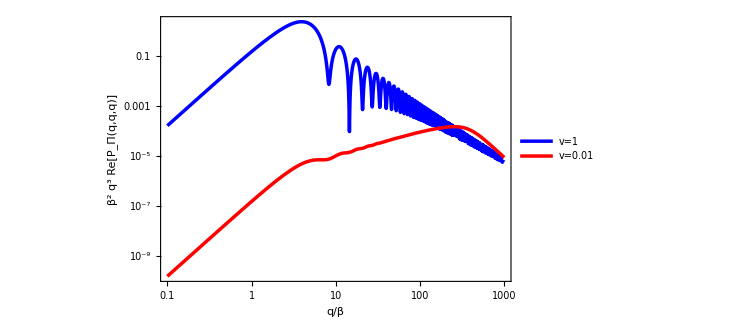

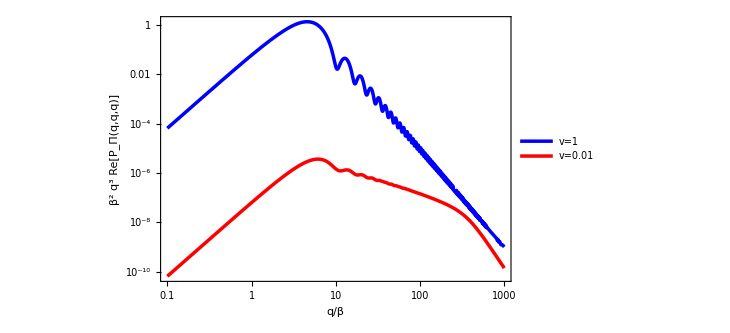

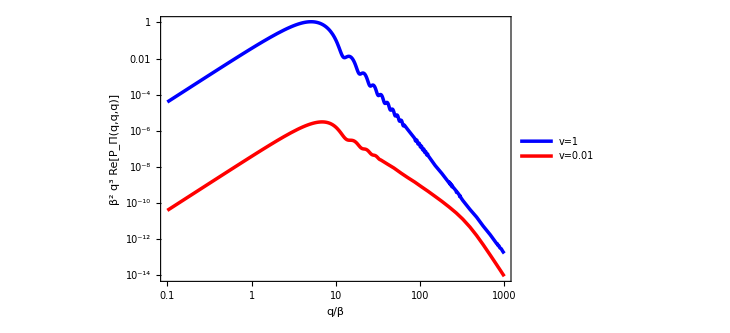

```mathematica
plotGWtemplate=LogLogPlot[{GWspectrum[k,k,1,1],GWspectrum[k,k,0.01,1]},{k,10^-1,10^3},PlotStyle->{{Blue,AbsoluteThickness[2.5]},{Red,AbsoluteThickness[2.5]}},AspectRatio->1/GoldenRatio,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],GridLines->None,FrameLabel->{Style[DisplayForm[FormBox[RowBox[{FormBox["q",TraditionalForm],"/",FormBox["β",TraditionalForm]}],TraditionalForm]],FontSize->16],Style[DisplayForm[FormBox[RowBox[{SuperscriptBox["β","2"],SuperscriptBox["q","3"]," ",FormBox["Re",TraditionalForm],"[",SubscriptBox["P","Π"],"(","q",",","q",",","q",")","]"}],TraditionalForm]],FontSize->16]},PlotLegends->Placed[LineLegend[{Style[DisplayForm[FormBox[RowBox[{"v","=","1"}],TraditionalForm]],FontSize->13],Style[
DisplayForm[FormBox[RowBox[{"v","=","0.01"}],TraditionalForm]],FontSize->13]},Background->White,FrameStyle->Directive[Black,AbsoluteThickness[0.8]],LegendLabel->None,LegendMargins->6,LegendMarkerSize->20],{0.82,0.78}],Exclusions->None,MaxRecursion->5,ImageSize->540]

LogLogPlot[{GWspectrum[k,k,1,2],GWspectrum[k,k,0.01,2]},{k,10^-1,10^3},PlotStyle->{{Blue,AbsoluteThickness[2.5]},{Red,AbsoluteThickness[2.5]}},AspectRatio->1/GoldenRatio,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],GridLines->None,FrameLabel->{Style[DisplayForm[FormBox[RowBox[{FormBox["q",TraditionalForm],"/",FormBox["β",TraditionalForm]}],TraditionalForm]],FontSize->16],Style[DisplayForm[FormBox[RowBox[{SuperscriptBox["β","2"],SuperscriptBox["q","3"]," ",FormBox["Re",TraditionalForm],"[",SubscriptBox["P","Π"],"(","q",",","q",",","q",")","]"}],TraditionalForm]],FontSize->16]},PlotLegends->Placed[LineLegend[{Style[DisplayForm[FormBox[RowBox[{"v","=","1"}],TraditionalForm]],FontSize->13],Style[
DisplayForm[FormBox[RowBox[{"v","=","0.01"}],TraditionalForm]],FontSize->13]},Background->White,FrameStyle->Directive[Black,AbsoluteThickness[0.8]],LegendLabel->None,LegendMargins->6,LegendMarkerSize->20],{0.82,0.78}],Exclusions->None,MaxRecursion->5,ImageSize->540]

LogLogPlot[{GWspectrum[k,k,1,3],GWspectrum[k,k,0.01,3]},{k,10^-1,10^3},PlotStyle->{{Blue,AbsoluteThickness[2.5]},{Red,AbsoluteThickness[2.5]}},AspectRatio->1/GoldenRatio,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],GridLines->None,FrameLabel->{Style[DisplayForm[FormBox[RowBox[{FormBox["q",TraditionalForm],"/",FormBox["β",TraditionalForm]}],TraditionalForm]],FontSize->16],Style[DisplayForm[FormBox[RowBox[{SuperscriptBox["β","2"],SuperscriptBox["q","3"]," ",FormBox["Re",TraditionalForm],"[",SubscriptBox["P","Π"],"(","q",",","q",",","q",")","]"}],TraditionalForm]],FontSize->16]},PlotLegends->Placed[LineLegend[{Style[DisplayForm[FormBox[RowBox[{"v","=","1"}],TraditionalForm]],FontSize->13],Style[
DisplayForm[FormBox[RowBox[{"v","=","0.01"}],TraditionalForm]],FontSize->13]},Background->White,FrameStyle->Directive[Black,AbsoluteThickness[0.8]],LegendLabel->None,LegendMargins->6,LegendMarkerSize->20],{0.82,0.78}],Exclusions->None,MaxRecursion->5,ImageSize->540]
(*
Export[FileNameJoin[{NotebookDirectory[],"GW_spectrum_template.pdf"}],plotGWtemplate];
*)
```

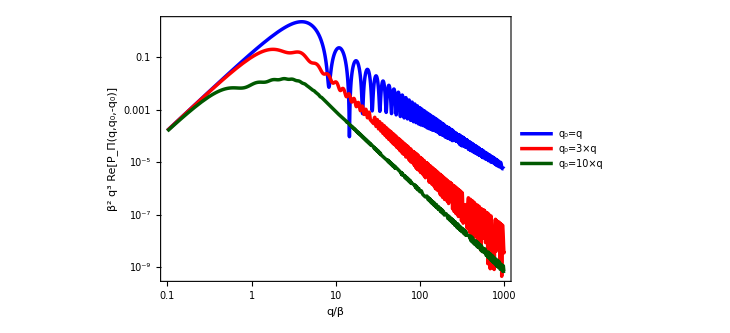

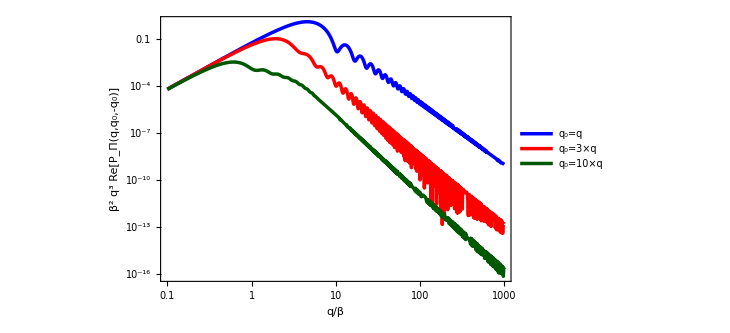

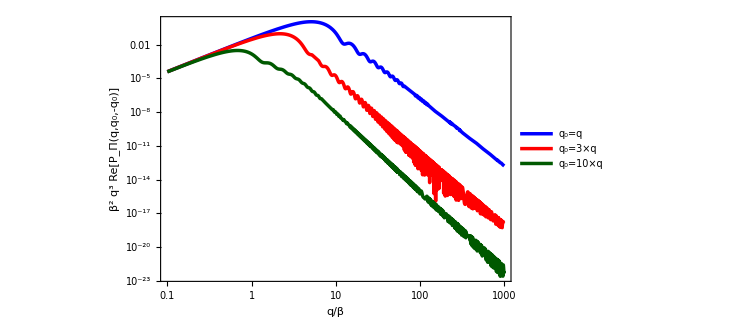

```mathematica
plotGWoffshell=LogLogPlot[{GWspectrum[k,k,1,1],GWspectrum[3*k,k,1,1],GWspectrum[10*k,k,1,1]},{k,10^-1,10^3},PlotStyle->{{Blue,AbsoluteThickness[2.5]},{Red,AbsoluteThickness[2.5]},{DarkGreen,AbsoluteThickness[2.5]}},AspectRatio->1/GoldenRatio,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],GridLines->None,FrameLabel->{Style[DisplayForm[FormBox[RowBox[{FormBox["q",TraditionalForm],"/",FormBox["β",TraditionalForm]}],TraditionalForm]],FontSize->16],Style[DisplayForm[FormBox[RowBox[{SuperscriptBox["β","2"],SuperscriptBox["q","3"]," ",FormBox["Re",TraditionalForm],"[",SubscriptBox["P","Π"],"(","q",",",SubscriptBox["q","0"],",",SubscriptBox["-q","0"],")","]"}],TraditionalForm]],FontSize->16]},PlotLegends->Placed[LineLegend[{Style[DisplayForm[FormBox[RowBox[{SubscriptBox["q","0"],"=","q"}],TraditionalForm]],FontSize->13],Style[DisplayForm[FormBox[RowBox[{SubscriptBox["q","0"],"=","3×q"}],TraditionalForm]],FontSize->13],Style[DisplayForm[FormBox[RowBox[{SubscriptBox["q","0"],"=","10×q"}],TraditionalForm]],FontSize->13]},Background->White,FrameStyle->Directive[Black,AbsoluteThickness[0.8]],LegendMargins->6,LegendMarkerSize->20,LabelStyle->Directive[FontFamily->"Times"]],{0.22,0.25} ],Exclusions->None,MaxRecursion->5,ImageSize->540]

LogLogPlot[{GWspectrum[k,k,1,2],GWspectrum[3*k,k,1,2],GWspectrum[10*k,k,1,2]},{k,10^-1,10^3},PlotStyle->{{Blue,AbsoluteThickness[2.5]},{Red,AbsoluteThickness[2.5]},{DarkGreen,AbsoluteThickness[2.5]}},AspectRatio->1/GoldenRatio,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],GridLines->None,FrameLabel->{Style[DisplayForm[FormBox[RowBox[{FormBox["q",TraditionalForm],"/",FormBox["β",TraditionalForm]}],TraditionalForm]],FontSize->16],Style[DisplayForm[FormBox[RowBox[{SuperscriptBox["β","2"],SuperscriptBox["q","3"]," ",FormBox["Re",TraditionalForm],"[",SubscriptBox["P","Π"],"(","q",",",SubscriptBox["q","0"],",",SubscriptBox["-q","0"],")","]"}],TraditionalForm]],FontSize->16]},PlotLegends->Placed[LineLegend[{Style[DisplayForm[FormBox[RowBox[{SubscriptBox["q","0"],"=","q"}],TraditionalForm]],FontSize->13],Style[DisplayForm[FormBox[RowBox[{SubscriptBox["q","0"],"=","3×q"}],TraditionalForm]],FontSize->13],Style[DisplayForm[FormBox[RowBox[{SubscriptBox["q","0"],"=","10×q"}],TraditionalForm]],FontSize->13]},Background->White,FrameStyle->Directive[Black,AbsoluteThickness[0.8]],LegendMargins->6,LegendMarkerSize->20,LabelStyle->Directive[FontFamily->"Times"]],{0.22,0.25} ],Exclusions->None,MaxRecursion->5,ImageSize->540]

LogLogPlot[{GWspectrum[k,k,1,3],GWspectrum[3*k,k,1,3],GWspectrum[10*k,k,1,3]},{k,10^-1,10^3},PlotStyle->{{Blue,AbsoluteThickness[2.5]},{Red,AbsoluteThickness[2.5]},{DarkGreen,AbsoluteThickness[2.5]}},AspectRatio->1/GoldenRatio,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],GridLines->None,FrameLabel->{Style[DisplayForm[FormBox[RowBox[{FormBox["q",TraditionalForm],"/",FormBox["β",TraditionalForm]}],TraditionalForm]],FontSize->16],Style[DisplayForm[FormBox[RowBox[{SuperscriptBox["β","2"],SuperscriptBox["q","3"]," ",FormBox["Re",TraditionalForm],"[",SubscriptBox["P","Π"],"(","q",",",SubscriptBox["q","0"],",",SubscriptBox["-q","0"],")","]"}],TraditionalForm]],FontSize->16]},PlotLegends->Placed[LineLegend[{Style[DisplayForm[FormBox[RowBox[{SubscriptBox["q","0"],"=","q"}],TraditionalForm]],FontSize->13],Style[DisplayForm[FormBox[RowBox[{SubscriptBox["q","0"],"=","3×q"}],TraditionalForm]],FontSize->13],Style[DisplayForm[FormBox[RowBox[{SubscriptBox["q","0"],"=","10×q"}],TraditionalForm]],FontSize->13]},Background->White,FrameStyle->Directive[Black,AbsoluteThickness[0.8]],LegendMargins->6,LegendMarkerSize->20,LabelStyle->Directive[FontFamily->"Times"]],{0.22,0.25} ],Exclusions->None,MaxRecursion->5,ImageSize->540]
(*
Export[FileNameJoin[{NotebookDirectory[],"GW_spectrum_template_offshell.pdf"}],plotGWoffshell];
*)
```

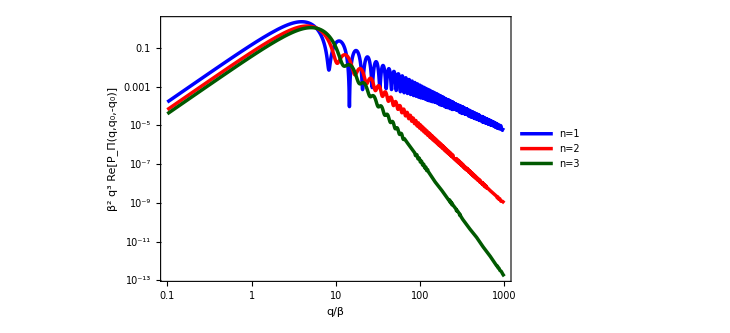

```mathematica
LogLogPlot[{GWspectrum[k,k,1,1],GWspectrum[k,k,1,2],GWspectrum[k,k,1,3]},{k,10^-1,10^3},PlotStyle->{{Blue,AbsoluteThickness[2.5]},{Red,AbsoluteThickness[2.5]},{DarkGreen,AbsoluteThickness[2.5]}},AspectRatio->1/GoldenRatio,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],GridLines->None,FrameLabel->{Style[DisplayForm[FormBox[RowBox[{FormBox["q",TraditionalForm],"/",FormBox["β",TraditionalForm]}],TraditionalForm]],FontSize->16],Style[DisplayForm[FormBox[RowBox[{SuperscriptBox["β","2"],SuperscriptBox["q","3"]," ",FormBox["Re",TraditionalForm],"[",SubscriptBox["P","Π"],"(","q",",",SubscriptBox["q","0"],",",SubscriptBox["-q","0"],")","]"}],TraditionalForm]],FontSize->16]},PlotLegends->Placed[LineLegend[{Style[DisplayForm[FormBox[RowBox[{"n","=","1"}],TraditionalForm]],FontSize->13],Style[DisplayForm[FormBox[RowBox[{"n","=","2"}],TraditionalForm]],FontSize->13],Style[DisplayForm[FormBox[RowBox[{"n","=","3"}],TraditionalForm]],FontSize->13]},Background->White,FrameStyle->Directive[Black,AbsoluteThickness[0.8]],LegendMargins->6,LegendMarkerSize->20,LabelStyle->Directive[FontFamily->"Times"]],{0.22,0.25} ],Exclusions->None,MaxRecursion->5,ImageSize->540]
```

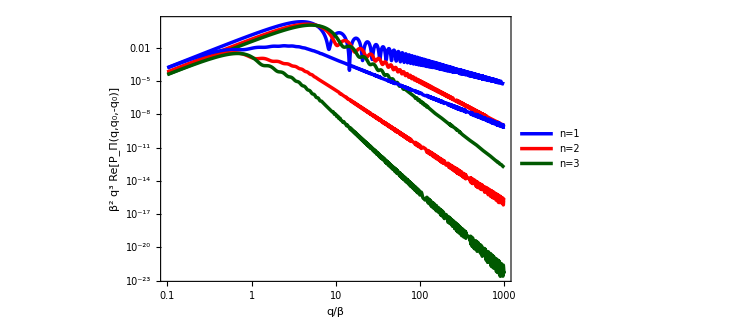

```mathematica
LogLogPlot[{GWspectrum[k,k,1,1],GWspectrum[k,k,1,2],GWspectrum[k,k,1,3],GWspectrum[10*k,k,1,1],GWspectrum[10*k,k,1,2],GWspectrum[10*k,k,1,3]},{k,10^-1,10^3},PlotStyle->{{Blue,AbsoluteThickness[2.5]},{Red,AbsoluteThickness[2.5]},{DarkGreen,AbsoluteThickness[2.5]},{Blue,AbsoluteThickness[2.5]},{Red,AbsoluteThickness[2.5]},{DarkGreen,AbsoluteThickness[2.5]}},AspectRatio->1/GoldenRatio,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],GridLines->None,FrameLabel->{Style[DisplayForm[FormBox[RowBox[{FormBox["q",TraditionalForm],"/",FormBox["β",TraditionalForm]}],TraditionalForm]],FontSize->16],Style[DisplayForm[FormBox[RowBox[{SuperscriptBox["β","2"],SuperscriptBox["q","3"]," ",FormBox["Re",TraditionalForm],"[",SubscriptBox["P","Π"],"(","q",",",SubscriptBox["q","0"],",",SubscriptBox["-q","0"],")","]"}],TraditionalForm]],FontSize->16]},PlotLegends->Placed[LineLegend[{Style[DisplayForm[FormBox[RowBox[{"n","=","1"}],TraditionalForm]],FontSize->13],Style[DisplayForm[FormBox[RowBox[{"n","=","2"}],TraditionalForm]],FontSize->13],Style[DisplayForm[FormBox[RowBox[{"n","=","3"}],TraditionalForm]],FontSize->13]},Background->White,FrameStyle->Directive[Black,AbsoluteThickness[0.8]],LegendMargins->6,LegendMarkerSize->20,LabelStyle->Directive[FontFamily->"Times"]],{0.22,0.25} ],Exclusions->None,MaxRecursion->5,ImageSize->540]
```